### Problem 1

```mathematica
Clear["Global*'"]
```

```mathematica
MFD=5.3*10^-3;(*mm*)
λ=635*10^-6;
f=7.5;
wreq=λ f/(Pi MFD)
```

0.286028

```mathematica
pos={9,18,27};
wx={.53,.65,.69}/10;(*in*)
data1=Transpose@{pos,wx};
λ=2.5*10^-5;
w[z_]:=w0 Sqrt[(1+((z+d) λ/(Pi w0^2))^2)];
vars1=FindFit[data1,w[x],{{w0,.01},{d,50}},x,Method->NMinimize]
wfit1[x_]=w[x]/.vars1;
(*the laser was measured to be 43.5in behind this zero*)
Mfree[L_]:=({{1, L}, {0, 1}});
Mlens[f_]:=({{1, 0}, {-1/f, 1}});
pos={9,18,27};
wx={.53,.65,.69}/10;(*in*)
data1=Transpose@{pos,wx};
λ=2.5*10^-5;
w[z_]:=w0 Sqrt[(1+((z+d) λ/(Pi w0^2))^2)];
vars1=FindFit[data1,w[x],{{w0,.01},{d,50}},x,Method->NMinimize]
wfit1[x_]=w[x]/.vars1;
```

{w0→0.00885803,d→50.6734}

{w0→0.00885803,d→50.6734}

0.224994

(-0.254 | 125.4
0. | -3.93701)

{0.0572014,{z→0.070461}}

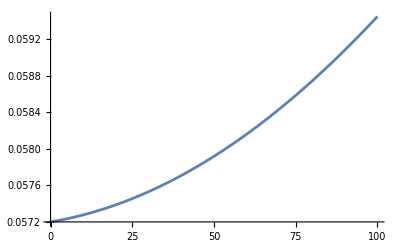

0.00104339

0.00762679

```mathematica
wmin=0.008858026394561114*25.4
fo=100;
fe=25.4;
(telescope=Mlens[fe].Mfree[fo+fe].Mlens[fo])//MatrixForm//Simplify
beam=M[inq[(23+50.673390832882795-43.5)*25.4,wmin],telescope];
minfunc[z_]:=M[beam,{{1,z},{0,1}}];
FindMinimum[{waist[minfunc[z]],z>=0},z]
Plot[waist[minfunc[z]],{z,0,100}]
wtemp=λ f/(Pi waist[beam])
λ/(Pi wtemp)
```

### Problem 5 Efficiency Calculations

```mathematica
wxx=10;
wyy=10;
P=2;(*measured max power*)
Inten[x_,y_]:=2*P/(Pi wxx wyy)E^-(2 x^2/wxx^2)E^-(2 y^2/wyy^2);
out=Integrate[Inten[x,y],{x,-5.3,5.3},{y,-5.3,5.3}];
Print["Total Efficiency: ",out/P*.86]
Print["Efficiency from geometric factors: ",out/P]
```

Total Efficiency: 0.434571

Efficiency from geometric factors0.505315